Computational Physics

# Title. Solitons

Paul Abbott

School of Physics, M013
The University of Western Australia
35 Stirling Highway
Crawley WA 6009, Australia
paul.c.abbott@uwa.edu.au

#### Pre-requisites

We modify Equal so that Listable operations are automatically applied to both sides of any equality:

```mathematica
Unprotect[Equal];
```

```mathematica
listableQ(f_):=MemberQ(Attributes(f),Listable)
```

```mathematica
Equal/: lhs:f_Symbol?listableQ[___, _Equal, ___] :=
        Thread[ Unevaluated[lhs], Equal ]
```

```mathematica
Protect[Equal];
```

Now, we can directly manipulate equations.

### References

Baumann G, Mathematica in Theoretical Physics, TELOS, Springer-Verlag, New York, 197-215, 1996.

Crandall R E, Mathematica for the Sciences, Addison-Wesley, Redwood City, 140-156, 1991.

Title.Section. Solitons

The Korteweg de Vries (KdV) equation, describing water waves in shallow channels, is given by

(∂u)/(∂t)-6 u (∂u)/(∂x)+(∂^3 u)/(∂x^3)=0,

where u(x,t) is the wave amplitude. In Mathematica notation, the differential operator reads

```mathematica
𝒟(u_):=(∂u)/(∂t)-6 u (∂u)/(∂x)+(∂^3 u)/(∂x^3);
```

### Title.Section.Subsection. One-soliton Solution

Title.Section.Exercise. Find a solution to the KdV equation (Title.Section.Equation) of the form a sech^2(x-b t) by selecting suitable values for a and b. Call your result u_1(x_,t_). Visualize (and animate) the time evolution of u_1(x,t) over x∈[-20,20] for t=-4,-3,…,4. What happens to the shape of the wave as a function of time? [7]

Substituting in a sech^2(x-b t),

```mathematica
𝒟(a sech^2(x-b t))//Simplify
```

-a tanh(b t-x) sech^4(b t-x) (12 a+(b-4) cosh(2 b t-2 x)+b+20)

we see that the term involving cosh(2 b t-2 x) is eliminated it b→4,

```mathematica
%/.b->4
```

-a (12 a+24) tanh(4 t-x) sech^4(4 t-x)

and the resulting expression vanishes if a→-2.

```mathematica
%/.a->-2
```

0

As a check:

```mathematica
Subscript[u, 1](x_,t_)=-2 sech^2(x-4 t);
```

```mathematica
𝒟(Subscript[u, 1](x,t))//Simplify
```

0

```mathematica
Manipulate[Plot[Subscript[u, 1](x,t),{x,-20,20},PlotRange->{-2.1,0}],{t,-4,4}]
```

The shape of the wave does not change with time.

Title.Section.Exercise. What is the velocity of an arbitrary wave of the form f(k x-ω t)? Determine the velocity of u_1(x,t) from its time evolution and compare it with the expected result. [2]

The velocity of a wave of the form f(k x-ω t) is c=ω/k=4/1. This agrees with the velocity determined from the time evolution. The peak of the wave moves 4 units in one second.

### Title.Section.Subsection. Two-soliton Solution

Title.Section.Exercise. Verify that u_2(x,t)=-(12 (4 cosh(8 t-2 x)+cosh(64 t-4 x)+3))/(3 cosh(28 t-x)+cosh(36 t-3 x))^2 is a “two-soliton” solution to the KdV equation (Title.Section.Equation). Visualize the time evolution of this solution over x∈[-40,40] for t=-2,-1.75,-1.5,…,1.75,2.  The meaning of the name “two-soliton” solution should become clear. [2]

```mathematica
Subscript[u, 2](x_,t_)=-(12 (4 cosh(8 t-2 x)+cosh(64 t-4 x)+3))/(3 cosh(28 t-x)+cosh(36 t-3 x))^2;
```

```mathematica
𝒟(Subscript[u, 2](x,t))//Simplify
```

0

Here we visualize the time evolution of this solution. It is clear that there are now two waves; one slow and one fast.

```mathematica
Manipulate[Plot[Subscript[u, 2](x,t),{x,-40,40},PlotRange->{-10,0.1}],{t,-2,2,0.25},SaveDefinitions->True]
```

Observe that the smaller slower soliton of the two-soliton solution appears identical to the one-soliton solution, but with a small phase shift.

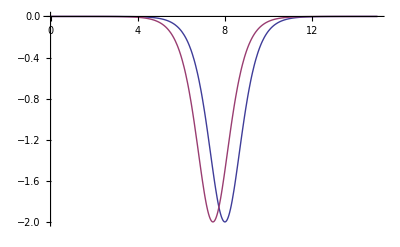

```mathematica
Plot[{Subscript[u, 1](x,2),Subscript[u, 2](x,2)},{x,0,15},PlotRange->All]
```

From your visualization of the two-soliton solution, you should find that the velocity of the smaller slower soliton is

```mathematica
Subscript[v, 1]=+4;
```

In a frame of reference moving with this velocity (x→x+v_1 t), the shape of the slow soliton as t→∞ is given as follows.

```mathematica
Subscript[u, 2,slow](x_,∞)=lim_(t->∞) TrigToExp[Subscript[u, 2](x+Subscript[v, 1] t ,t)]
```

-(24 ⅇ^(2 x))/((3 ⅇ^(2 x)+1)^2)

Title.Section.Exercise. Plot u_(2,slow)(x,∞) and u_1(x,0) together for x∈[-5,5]. Determine the exact phase-shift by solving u_1(x+ϕ,0)=u_(2,slow)(x,∞). Verify that your result agrees with the plot. [4]

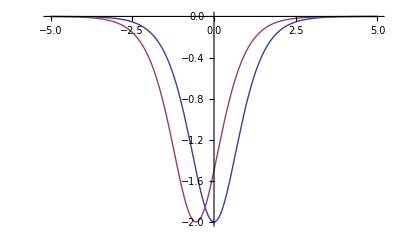

```mathematica
Plot[{Subscript[u, 1](x,0),Subscript[u, 2,slow](x,∞)},{x,-5,5},PlotRange->All]
```

Comparing this result to the one-soliton solution with a phase-shift ϕ, that is

```mathematica
Subscript[u, 1](x+ϕ,0)==Subscript[u, 2,slow](x,∞)//TrigToExp
```

-8/((ⅇ^(-x-ϕ)+ⅇ^(x+ϕ))^2)==-(24 ⅇ^(2 x))/((3 ⅇ^(2 x)+1)^2)

and solving for ϕ,

```mathematica
FullSimplify[Solve[%,ϕ],x>0]
```

{{ϕ→ConditionalExpression[ⅈ π (2 c_1+1)-2 x-(log(3))/2,c_1∈ℤ]},{ϕ→ConditionalExpression[2 ⅈ π c_1-2 x-(log(3))/2,c_1∈ℤ]},{ϕ→ConditionalExpression[1/2 (log(3)+2 ⅈ π (2 c_1+1)),c_1∈ℤ]},{ϕ→ConditionalExpression[1/2 (log(3)+4 ⅈ π c_1),c_1∈ℤ]}}

we find that ϕ=(log(3))/2≈0.549306. This agrees with the above plot.

Title.Section.Exercise. Determine the velocity of the taller faster soliton, v_2, and use this to find the shape of the fast soliton as t→∞. [2]

```mathematica
Subscript[v, 2]=+16;
```

```mathematica
Subscript[u, 2,fast](x_,∞)=lim_(t->∞) TrigToExp[Subscript[u, 2](x+Subscript[v, 2] t,t)]
```

-(96 ⅇ^(4 x))/((ⅇ^(4 x)+3)^2)

### Title.Section.Subsection. n-soliton solution

There is an interesting relationship between the soliton solutions of the KdV equation (Section.Equation) and the Schrödinger equation. Using this relationship, the n-soliton solution can be generated in an exact way.

Initial values (t=0) of the one- and two-soliton solutions read.

```mathematica
Subscript[u, 1](x,0)
```

-2 sech^2(x)

```mathematica
Subscript[u, 2](x,0)//Simplify
```

-6 sech^2(x)

It turns out that the initial value of the n-soliton solution is u_n(x,0)=-n(n+1)sech^2(x)=2𝒱_n(x). If 𝒱_n(x) is interpreted as the potential of the Schrödinger equation, that is

-1/2(∂^2 ψ(x))/(∂x^2)-1/2 n(n+1)sech^2(x)ψ(x)=ℰ ψ(x),

the (unnormalized) solution is

```mathematica
Subscript[ψ, n_,m_](x_)=Subscript[P, n]^m(tanh(x));
```

where P_n^m(z) is the associated Legendre function, and the energy is ℰ_m=-m^2/2. For each n, there exists n bound states with 1≤m≤n.

Title.Section.Exercise. Verify that each ψ_(n,m)(x) satisfies the Schrödinger equation (Title.Section.Equation) for 1≤m≤n≤4. [2]

```mathematica
Subscript[𝒱, n_](x_)=-(n (n+1))/2 sech^2(x);
```

```mathematica
Subscript[ℰ, m_]=-m^2/2;
```

```mathematica
Table[Simplify[-1/2(∂^2 Subscript[ψ, n,m](x))/(∂x^2)+Subscript[𝒱, n](x) Subscript[ψ, n,m](x)==Subscript[ℰ, m] Subscript[ψ, n,m](x),x∈ℝ],{n,4},{m,n}]//Flatten//Union
```

{True}

Title.Section.Exercise. Use dynamic programming (𝒩/:𝒩_(n_,m_):=𝒩/:𝒩_(n,m)=…), to compute and save the normalization constants determined by requiring 𝒩_(n,m)^2∫_(-∞)^∞ (ψ_(n,m)(x))^2 ⅆx=1. Determine the normalization constants for 1≤m≤n≤4. [2]

```mathematica
𝒩/:Subscript[𝒩, n_,m_]:=𝒩/:Subscript[𝒩, n,m]=1/√(∫_(-∞)^∞ (Subscript[ψ, n,m](x))^2 ⅆx)
```

```mathematica
Table[Subscript[𝒩, n,m]^2,{n,4},{m,n}]//Grid
```

1/2 |  |  | 
1/6 | 1/12 |  | 
1/12 | 1/60 | 1/240 | 
1/20 | 1/180 | 1/1680 | 1/10080

Title.Section.Exercise. On one plot, display the potential V_n(x) together with the normalized eigenfunctions, shifted downwards by the associated energy, 𝒩_(n,m)^2(ψ_(n,m)(x))^2+ℰ_m, for 1≤n≤5 and 1≤m≤n. [3]

```mathematica
Manipulate[Plot[Evaluate[Join[Table[Subscript[𝒩, n,m]^2(Subscript[ψ, n,m](x))^2+Subscript[ℰ, m],{m,n}],{Subscript[𝒱, n](x)}]],{x,-5,5},Filling->Table[m->Subscript[ℰ, m],{m,n}]],{n,Range[5]},SaveDefinitions->True]
```

The next step in determining the n-soliton solution (much theory omitted here) is to form the n×n matrix, 𝒜_n, whose coefficients are

```mathematica
Subscript[𝒜, n_,m_,k_]:=Subscript[δ, m,k]+Subscript[c, n,m]^2/(m+k)ⅇ^(8 m^3 t-(m+k)x)
```

where

```mathematica
Subscript[c, n_,m_]:=Subscript[c, n,m]=lim_(x->∞) Expand[Subscript[𝒩, n,m] Subscript[ψ, n,m](x) ⅇ^(m x)]
```

Finally, the n-soliton solution is given by

u_n(x,t)=-2 (∂^2 log(|𝒜_n|))/(∂x^2),

where |𝒜_n| is the determinant of 𝒜_n. For example, the two-soliton matrix is

```mathematica
Subscript[𝒜, 2]=Table[Subscript[𝒜, 2,m,k],{m,2},{k,2}]
```

(1+3 ⅇ^(8 t-2 x) | 2 ⅇ^(8 t-3 x)
4 ⅇ^(64 t-3 x) | 1+3 ⅇ^(64 t-4 x))

and the two-soliton solution is

```mathematica
-2 (∂^2 log(|Subscript[𝒜, 2]|))/(∂x^2)
```

-2 ((36 ⅇ^(72 t-6 x)+48 ⅇ^(64 t-4 x)+12 ⅇ^(8 t-2 x))/(ⅇ^(72 t-6 x)+3 ⅇ^(64 t-4 x)+3 ⅇ^(8 t-2 x)+1)-((-6 ⅇ^(72 t-6 x)-12 ⅇ^(64 t-4 x)-6 ⅇ^(8 t-2 x))^2)/((ⅇ^(72 t-6 x)+3 ⅇ^(64 t-4 x)+3 ⅇ^(8 t-2 x)+1)^2))

We compare this result with u_2(x,t) given above in question (Section.Exercise)

```mathematica
Simplify[%==Subscript[u, 2](x,t)]
```

True

Title.Section.Exercise. Compute the three-soliton solution, u_3(x,t) to the KdV equation (Title.Section.Equation). Visualize the time evolution of u_3(x,t) for t∈[-1,1] and x∈[-20,20] using ContourPlot. [2]

Three-soliton matrix:

```mathematica
Subscript[𝒜, 3]=Table[Subscript[𝒜, 3,j,k],{j,3},{k,3}]
```

(1+6 ⅇ^(8 t-2 x) | 4 ⅇ^(8 t-3 x) | 3 ⅇ^(8 t-4 x)
20 ⅇ^(64 t-3 x) | 1+15 ⅇ^(64 t-4 x) | 12 ⅇ^(64 t-5 x)
15 ⅇ^(216 t-4 x) | 12 ⅇ^(216 t-5 x) | 1+10 ⅇ^(216 t-6 x))

Three-soliton solution:

```mathematica
Subscript[u, 3](x_,t_)=-2 (∂^2 log(|Subscript[𝒜, 3]|))/(∂x^2)//Simplify
```

-((48 ⅇ^(8 t+2 x) (30 ⅇ^(16 (4 t+x))+15 ⅇ^(16 (13 t+x))+252 ⅇ^(10 (28 t+x))+50 ⅇ^(8 (36 t+x))+135 ⅇ^(8 (42 t+x))+25 ⅇ^(8 (54 t+x))+15 ⅇ^(4 (88 t+x))+10 ⅇ^(504 t+2 x)+30 ⅇ^(496 t+4 x)+80 ⅇ^(344 t+6 x)+40 ⅇ^(488 t+6 x)+25 ⅇ^(128 t+12 x)+135 ⅇ^(224 t+12 x)+50 ⅇ^(272 t+12 x)+40 ⅇ^(72 t+14 x)+80 ⅇ^(216 t+14 x)+10 ⅇ^(56 t+18 x)+ⅇ^(560 t)+ⅇ^(20 x)))/(15 ⅇ^(8 (8 t+x))+10 ⅇ^(6 (36 t+x))+15 ⅇ^(4 (56 t+x))+6 ⅇ^(280 t+2 x)+10 ⅇ^(72 t+6 x)+6 ⅇ^(8 t+10 x)+ⅇ^(288 t)+ⅇ^(12 x))^2)

```mathematica
ContourPlot[-Subscript[u, 3](x,t),{t,-1,1},{x,-20,20},PlotPoints->60,Contours->10 ⅇ^(-Range[0,5])]
```

-Graphics-

```mathematica
Plot3D[log(-Subscript[u, 3](x,t)),{t,-2,2},{x,-40,40},Mesh->False,PlotPoints->60,PlotRange->All]
```

-Graphics3D-

Title.Section.Exercise. Determine the exact phase-shift of the slowest soliton by comparing it with u_1(x+ϕ,0). [2]

The slowest soliton again has

```mathematica
Subscript[v, 1]=4;
```

so

```mathematica
Subscript[u, 3,slow](x_,∞)=lim_(t->∞) Subscript[u, 3](x+t Subscript[v, 1],t)
```

-(48 ⅇ^(2 x))/((6 ⅇ^(2 x)+1)^2)

Equating this to u_1(x+ϕ,0),

```mathematica
TrigToExp[Subscript[u, 1](x+ϕ,0)]==Subscript[u, 3,slow](x,∞)
```

-8/((ⅇ^(-x-ϕ)+ⅇ^(x+ϕ))^2)==-(48 ⅇ^(2 x))/((6 ⅇ^(2 x)+1)^2)

and solving for ϕ,

```mathematica
FullSimplify[Solve[%,ϕ],x>0]
```

{{ϕ→ConditionalExpression[ⅈ π (2 c_1+1)-2 x-(log(6))/2,c_1∈ℤ]},{ϕ→ConditionalExpression[2 ⅈ π c_1-2 x-(log(6))/2,c_1∈ℤ]},{ϕ→ConditionalExpression[1/2 (log(6)+2 ⅈ π (2 c_1+1)),c_1∈ℤ]},{ϕ→ConditionalExpression[1/2 (log(6)+4 ⅈ π c_1),c_1∈ℤ]}}

we find that ϕ=(log(6))/2≈0.89588.

Title.Section.Exercise. Determine the velocity of the fastest soliton and use this to find its shape as t→∞. [2]

```mathematica
Subscript[v, 3]=36;
```

```mathematica
Subscript[u, 3,fast](x_,∞)=lim_(t->∞) Subscript[u, 3](x+Subscript[v, 3] t,t)
```

-(720 ⅇ^(6 x))/((ⅇ^(6 x)+10)^2)

## Title.Section. Conservation Laws

A continuity equation, relating a general density ρ and its corresponding current J, of the form

∂_t ρ+∂_x J=0,

leads to a related conservation law. If both ρ and J depend on t, u, ∂u/∂x, ∂^2 u/∂x^2, … but not on ∂u/∂t, and J vanishes as x→±∞, integrating equation (Title.Section.Equation) over x∈(-∞,∞), leads to

∂_t ∫_(-∞)^∞ ρⅆx=0⇒∫_(-∞)^∞ ρⅆx=constant.

For example, the KdV equation (Title.Section.Equation) is already in the form of the continuity equation (Title.Section.Equation) with the density

```mathematica
ρ=u(x,t);
```

if the corresponding current J, is

```mathematica
J=∫((∂^3 u(x,t))/(∂x^3)-6 u(x,t) (∂u(x,t))/(∂x))ⅆx
```

u^(2,0)(x,t)-3 (u(x,t))^2

because

```mathematica
D[ρ, t]+D[J, x]==𝒟(u(x,t))
```

True

Hence, we conclude from the conservation equation (Title.Section.Equation) that ∫_(-∞)^∞ u(x,t)ⅆx=constant for solutions to the KdV equation (Title.Section.Equation) satisfying u(±∞,t)=0. Physically, this conservation law expresses conservation of mass.

Title.Section.Exercise. Verify that u_1(x,t) satisfies the conservation law, ∫_(-∞)^∞ u(x,t)ⅆx=constant. [1]

```mathematica
Assuming[t∈ℝ,∫_(-∞)^∞ Subscript[u, 1](x,t)ⅆx]
```

-4

Title.Section.Exercise. For the density ρ=∫u(x,t)∂_t u(x,t)ⅆt, find the corresponding current, J, and determine the associated (momentum) conservation law. Verify that u_1(x,t) satisfies this conservation law. [3]

For

```mathematica
ρ=∫u(x,t)D[u(x,t), t]ⅆt
```

1/2 (u(x,t))^2

appealing to the KdV equation (Title.Section.Equation), the associated current is

```mathematica
J=∫u(x,t) ((∂^3 u(x,t))/(∂x^3)-6 u(x,t) (∂u(x,t))/(∂x))ⅆx
```

u^(2,0)(x,t) u(x,t)-1/2 (u^(1,0)(x,t))^2-2 (u(x,t))^3

since, by construction,

```mathematica
Simplify[D[ρ, t]+D[J, x]]==u(x,t)𝒟(u(x,t))
```

True

The conservation law is 1/2∫_(-∞)^∞ (u(x,t))^2 ⅆx=constant. u_1(x,t) satisfies this conservation law.

```mathematica
Assuming[t∈ℝ,1/2∫_(-∞)^∞ (Subscript[u, 1](x,t))^2 ⅆx]
```

8/3

Title.Section.Exercise. For the (energy) density ρ=(u(x,t))^3+1/2 (u^(1,0)(x,t))^2, obtain and simplify the corresponding current (Hint: you will need to use the KdV equation (Title.Section.Equation) and its derivative with respect to x to eliminate the terms in ∂_t ρ involving time derivatives). Determine the associated conservation law, and verify that it is satisfied by u_1(x,t). [6]

For

```mathematica
ρ=(u(x,t))^3+1/2 (Derivative[1,0][u](x,t))^2;
```

computing ∂_t ρ

```mathematica
D[ρ, t]
```

3 u^(0,1)(x,t) (u(x,t))^2+u^(1,0)(x,t) u^(1,1)(x,t)

we see that it involves u^(0,1)(x,t) and u^(1,1)(x,t). We eliminate these time derivatives using the KdV equation (Title.Section.Equation) and its derivative with respect to x.

```mathematica
tsol=First[Solve[{𝒟(u(x,t))==0,(∂𝒟(u(x,t)))/(∂x)==0},{Derivative[0,1][u](x,t),Derivative[1,1][u](x,t)}]]
```

{u^(0,1)(x,t)→6 u(x,t) u^(1,0)(x,t)-u^(3,0)(x,t),u^(1,1)(x,t)→6 (u^(1,0)(x,t))^2+6 u(x,t) u^(2,0)(x,t)-u^(4,0)(x,t)}

```mathematica
D[ρ, t]/.tsol
```

3 (6 u(x,t) u^(1,0)(x,t)-u^(3,0)(x,t)) (u(x,t))^2+u^(1,0)(x,t) (6 (u^(1,0)(x,t))^2+6 u(x,t) u^(2,0)(x,t)-u^(4,0)(x,t))

Integrating the negative of this expression with respect to x yields the corresponding current.

```mathematica
J=∫-%ⅆx
```

3 u^(2,0)(x,t) (u(x,t))^2-6 (u^(1,0)(x,t))^2 u(x,t)-1/2 (u^(2,0)(x,t))^2+u^(1,0)(x,t) u^(3,0)(x,t)-9/2 (u(x,t))^4

As a check, we verify that the continuity equation (Title.Section.Equation) is satisfied.

```mathematica
D[ρ, t]+D[J, x]/.tsol//Simplify
```

0

The associated conservation law is

∫_(-∞)^∞ ρⅆx=∫_(-∞)^∞ ((u(x,t))^3+1/2 (u^(1,0)(x,t))^2)ⅆx=constant.

We now verify that u_1(x,t) satisfies this law. The density becomes

```mathematica
ρ/.u->Subscript[u, 1]//FullSimplify
```

4 (cosh(8 t-2 x)-3) sech^6(4 t-x)

```mathematica
Assuming[t∈ℝ,∫_(-∞)^∞ 4 (cosh(8 t-2 x)-3) sech^6(4 t-x)ⅆx]
```

-32/5